The role of edible habitat complexity in food webs (P2)

Eden Forbes, 2025 - 2026

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Quiet[<<"C:\Users\eforb\OneDrive\Desktop\RESEARCH\CODEBASE\Dynamica\Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## Building Block Visualizers

```mathematica
T2[x_]:=(595/(30+ x));
```

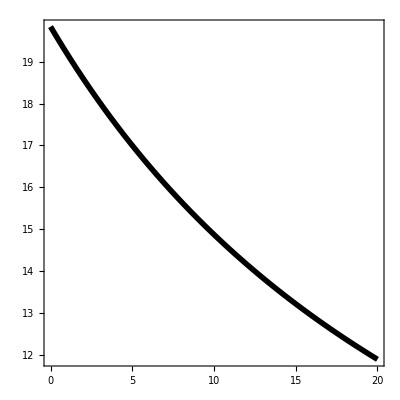

```mathematica
Plot[T2[x],{x,0,20},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,All},Frame->True,LabelStyle->{Black,20},AspectRatio->1
]
```

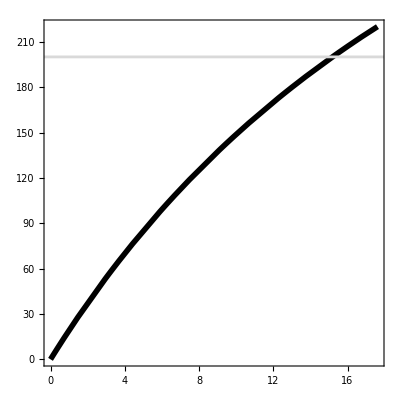

```mathematica
Plot[T2[x]*x,{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,220}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
β[rat_,steep_]:= (rat)^steep/((rat)^steep+α^steep); (* When the ratio is 10:1 (1),  start eating Dreissena *)
```

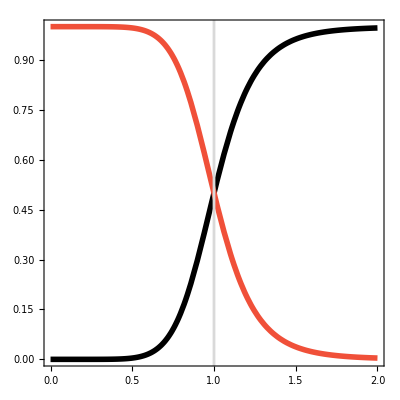

```mathematica
Show[
Plot[β[x,8]/.{α->1},{x,0,2},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
(*Plot[β[x,1]/.{α->1},{x,0,2},PlotStyle->{Black,Dashed,Thickness[0.01]},PlotRange->All],*)
Plot[1-β[x,8]/.{α->1},{x,0,2},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},PlotRange->All],
(*Plot[1-β[x,1]/.{α->1},{x,0,2},PlotStyle->{Blue,Dashed,Thickness[0.01]},PlotRange->All],*)
Frame->True,LabelStyle->{Black,20},AspectRatio->1,AxesOrigin->{0,0},GridLines->{{1},{}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
T2B[x_]:=((595 β[1,4])/(30+ x β[1,4]));
```

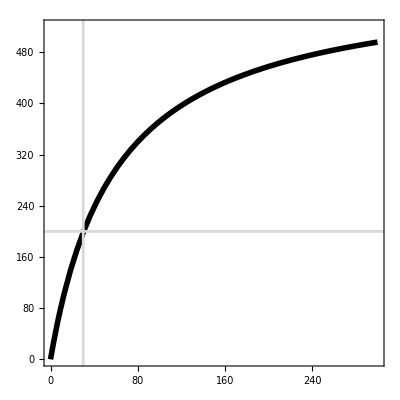

```mathematica
Plot[T2B[x]*x/.{α->1},{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,520}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]]
```

## HC

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
β[V_,Z_]:= (V/Z)^ω/((V/Z)^ω+α^ω);
```

```mathematica
FULL = DynamicalSystem[{
r*(1+δ M/kz)*V*(1 - V/(kv*(1+δ M/kz)))-((fvp β[V,M])/(hvp+ β[V,M] V))*V*P - dv V,
((yv ep)/yp)*((fvp β[V,M])/(hvp+ β[V,M] V))*V*P - dp*P,
b M (1-J/kz)-g J - dj J,
g J (1-M/kz)- dm M
},
{{V,-0.01,10000},{P,-0.01,100}, {J,-0.01,10000},{M,-0.01,10000}},
{{r,0,100},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0.06,0.12},{hvp,0,1},{fvp,0,1},{dp,0.0001,0.008},{yp,0,10000},
{α,0.001,1},{ω,1,4},{δ,0,4},
{b,1000,1500},{g,0.0001,1000},{kz,0.001,100},{kv,1,2000},{dj,1/730,1/182},{dm,0.0001,1}
}]
FULL = FULL/.{b->1370,g->1/270,dj->1/365,dm->1/1460,r->0.1,kz->200,kv->1000,dv->1/30, yv->0.67,ep->0.09,hvp->30, fvp->0.08*4900/0.67,dp->0.004, yp->4900,α->1,ω->4,δ->2};
```

DynamicalSystem[«4 ODEs»,{V,P,J,M},{r,dv,yv,ep,hvp,fvp,dp,yp,α,ω,δ,b,g,kz,kv,dj,dm}]

```mathematica
DisplayBifurcationDiagram[FULL,dp,StateVariables->{V,P}, MaxSteps->Infinity, MinStepSize->0.1]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={0,0,199.999,168.786,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={2354.53,0,199.999,168.786,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={2354.53,0,199.999,168.786,0.008}

-Graphics3D-

{BifurcationPoint[Branch,{0,0,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}],BifurcationPoint[Hopf,{161.140886607949,0.0851945649110097,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.0051054035533856,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}],BifurcationPoint[Hopf,{1162.22918362777,0.242961746407869,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.00701874822049626,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}]}

#### Funcs

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2; dp = 0.004;
```

```mathematica
TS=NDSolveValue[
{ V'[t]==r*V[t]*(1 - V[t]/kv)-(fvp/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*(fvp/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],
Pplot'[t] == 100*P[t] - Pplot[t],

V[0]==1000,P[0]==1, Pplot[0]==0
},{V,Pplot},{t,0,10000}];
(*TS2=NDSolveValue[
{ V'[t]==r*(1+δ M[t]/kz)*V[t]*(1 - V[t]/(kv*(1+δ M[t]/kz)))-((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],
J'[t]==b M[t](1-J[t]/kz) -g J[t] - dj J[t],
M'[t]==g J[t](1-M[t]/kz)- dm M[t],

V[0]==680,P[0]==0.5,J[0]==50, M[0]==50, 
WhenEvent[t==5500,{V[t]->680,P[t]->0.000008,J[t]->1,M[t]->1}]
},{V,P,J,M},{t,0,10000}];*)
```

NDSolveValue::ndsz: At t == 2069.94, step size is effectively zero; singularity or stiff system suspected.

#### Plots

InterpolatingFunction::dmval: Input value {2500.} lies outside the range of data in the interpolating function. Extrapolation will be used.

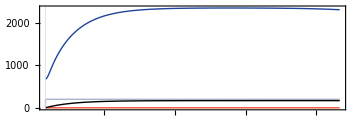

```mathematica
Show[
Plot[Evaluate[#[t]& /@TS],{t,2500,5500},PlotRange->All,ImageSize->Medium,
 PlotStyle->{{RGBColor["#1F449C"],Thick},{RGBColor["#F05039"],Thick},{RGBColor["#A8B6CC"],Thick},{Black,Thick}},
PlotPoints->1000],
Plot[Evaluate[#[t]& /@TS2],{t,5500,8000},PlotRange->All,ImageSize->Medium,
 PlotStyle->{{RGBColor["#1F449C"],Thick},{RGBColor["#F05039"],Thick},{RGBColor["#A8B6CC"],Thick},{Black,Thick}},
PlotPoints->1000],
TicksStyle->10,AxesOrigin->{2500,-20},
AspectRatio->1/3, LabelStyle->16, Frame->True,  FrameStyle->Black,
GridLines->{{5500},{}},GridLinesStyle->{Dashed,Thick}
]
```

## PCHART

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
dV = r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+ V β[V,M]))*V*P - dv V;
dP = ((yv ep)/yp)*((fvp β[V,M])/(hvp+ V β[V,M]))*V*P - dp*P ;
dJ = b M (1-J/kz)-g J - dj J;
dM = g J (1-M/kz)- dm M;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J13 = FullSimplify[D[dV,J]];
J14 = FullSimplify[D[dV,M]];
```

```mathematica
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
J23 = FullSimplify[D[dP,J]];
J24 = FullSimplify[D[dP,M]];
```

```mathematica
J31 = FullSimplify[D[dJ,V]];
J32 = FullSimplify[D[dJ,P]];
J33 = FullSimplify[D[dJ,J]];
J34 = FullSimplify[D[dJ,M]];
```

```mathematica
J41 = FullSimplify[D[dM,V]];
J42 = FullSimplify[D[dM,P]];
J43 = FullSimplify[D[dM,J]];
J44 = FullSimplify[D[dM,M]];
```

```mathematica
JM = {{J11,J12,J13,J14},{J21,J22,J23,J24},{J31,J32,J33,J34},{J41,J42,J43,J44}};
JM//MatrixForm
```

(-dv+r (1-(2 V)/kv+(M δ)/kz)-(fvp hvp P (V/M)^ω ((V/M)^ω+α^ω (1+ω)))/(((V/M)^ω (hvp+V)+hvp α^ω)^2) | -(fvp V (V/M)^ω)/((V/M)^ω (hvp+V)+hvp α^ω) | 0 | (V (M r (V/M)^(2 ω) (hvp+V)^2 δ+hvp^2 M r α^(2 ω) δ+hvp (V/M)^ω α^ω (2 M r (hvp+V) δ+fvp kz P ω)))/(kz M ((V/M)^ω (hvp+V)+hvp α^ω)^2)
(ep fvp hvp P (V/M)^ω yv ((V/M)^ω+α^ω (1+ω)))/(yp ((V/M)^ω (hvp+V)+hvp α^ω)^2) | -dp+(ep fvp V (V/M)^ω yv)/((V/M)^ω (hvp+V) yp+hvp yp α^ω) | 0 | -(ep fvp hvp P (V/M)^(1+ω) yv α^ω ω)/(yp ((V/M)^ω (hvp+V)+hvp α^ω)^2)
0 | 0 | -((dj+g) kz+b M)/kz | b-(b J)/kz
0 | 0 | g-(g M)/kz | -(g J+dm kz)/kz)

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}};
DJac//MatrixForm
```

(jVV | jVP | 0 | jVM
jPV | jPP | 0 | jPM
0 | 0 | jJJ | jJM
0 | 0 | jMJ | jMM)

```mathematica
Expand[CharacteristicPolynomial[DJac,x]]
```

General::ivar: {1,2} is not a valid variable.

CharacteristicPolynomial[{{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}},{1,2}]

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jJJ+jMM+jPP+jVV

```mathematica
L1 = J11+J22+J33+J44;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22)+(J43*J34-J33*J44)+(-J11*J44)+(-J11*J33)+(-J22*J44)+(-J22*J33);
```

#### Feedback Level 3

```mathematica
L3 = -(J34 J43 J22 -J33 J44 J22 + J33 J21 J12 + J44 J21 J12 + J34 J43 J11 - J33 J44 J11 - J33 J22 J11 - J44 J22 J11);
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJM jMJ jPP jVV+jJJ jMM jPP jVV

```mathematica
L4 =-(J34 J43 J12 J21-J33 J44 J12 J21-J34 J43 J22 J11+J11 J22 J33 J44);
```

#### Oscillation Criterion

```mathematica
OC = ((L1*L2+L3)*L3)/L1^2-L4;
```

### CHART - dp

```mathematica
Clear[dp]
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2;
```

```mathematica
solsPP= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsPP[[5]]/.dp->0.004
```

{V→133.453,P→0.0911913,J→199.999,M→168.786}

```mathematica
Vp = Re[solsPP[[3,1,2]]];
Jp = Re[solsPP[[3,3,2]]];
Mp = Re[solsPP[[3,4,2]]];

Vo = Re[solsPP[[5,1,2]]];
Po = Re[solsPP[[5,2,2]]];
Jo = Re[solsPP[[5,3,2]]];
Mo = Re[solsPP[[5,4,2]]];

P0=(((yv ep)/yp)*((fvp β[Vp,Mp])/(hvp+ Vp β[Vp,Mp]))*Vp)/dp;
```

```mathematica
FindRoot[P0==1,{dp,0.065}]
```

{dp→0.00710941}

#### Population EQ

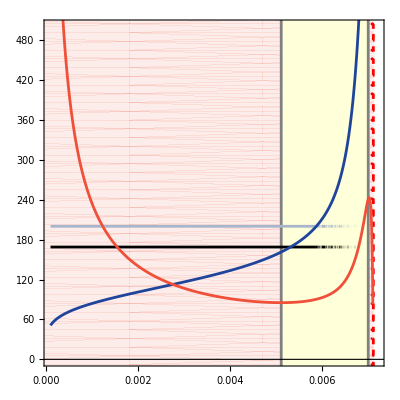

```mathematica
Show[
RegionPlot[0.00711> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.00511,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[Jo,{dp,0.0001,0.0071},PlotStyle->RGBColor["#A8B6CC"], PlotPoints->400],
Plot[Mo,{dp,0.0001,0.0071},PlotStyle->Black, PlotPoints->400],
Plot[Vo,{dp,0.0001,0.0071},PlotStyle->RGBColor["#1F449C"], PlotPoints->400, PlotRange->All],
Plot[Po*1000,{dp,0.00,0.0071},PlotStyle->RGBColor["#F05039"], PlotPoints->400,PlotRange->All],

Frame->True,FrameTicks->{{All,{{0,"0.0"},{100,"0.1"},{200,"0.2"},{300,"0.3"},{400,"0.4"},{500,"0.5"}}},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{0,500}}]
```

#### Population Mean/Min/Max

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
min = 0.00510; max =0.007; gran = 0.0001;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,dp->i*gran},{{58.64,0.036,49.99,42.196}},200000,MaxSteps->500000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,dp->i*gran},{Last[First[$Trajectories]]},20000, MaxSteps->Infinity,MaxStepSize->0.1, PlotPoints->1000];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[0.00711> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,2500}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

LogPlot[Jo,{dp,0.001,0.0071},PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}, PlotPoints->400],
LogPlot[Mo,{dp,0.001,0.0071},PlotStyle->{Black,Thickness[0.01]}, PlotPoints->400],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dotted}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dotted}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],

LogPlot[Vo,{dp,0.001,0.00511},PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}, PlotPoints->400],
LogPlot[Po*1000,{dp,0.001,0.00511},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}, PlotPoints->400,PlotRange->All],
LogPlot[Vo,{dp,0.007,0.0071},PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}, PlotPoints->400],
LogPlot[Po*1000,{dp,0.007,0.0071},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}, PlotPoints->400,PlotRange->All],


Frame->True,(*FrameTicks->{{All,{{0,"0"},{100,"0.02"},{200,"0.04"},{300,"0.06"},{400,"0.08"},{500,"0.10"},{600,"0.12"},{700,"0.14"}}},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},*)FrameTicksStyle->Black,
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0.001,0.0072},{4,7.6}}]
```

-Graphics-

#### Invert Density Dependence

```mathematica
IDD = FullSimplify[D[dV/V,V]]
```

-r/kv+(fvp P (V/M)^ω (V (V/M)^ω-hvp α^ω ω))/(V ((V/M)^ω (hvp+V)+hvp α^ω)^2)

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2;
```

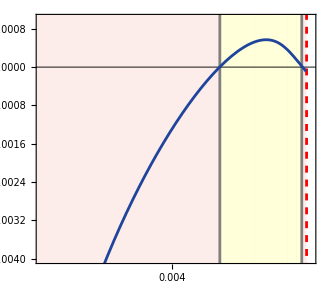

```mathematica
Show[
RegionPlot[0.00711> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IDD/.{V->Vo,P->Po, J->Jo, M->Mo},{dp,0.0001,0.0071 }, PlotStyle->RGBColor["#1F449C"]],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.0072},{-0.004,0.001}}]
```

#### MAIN LOOPS

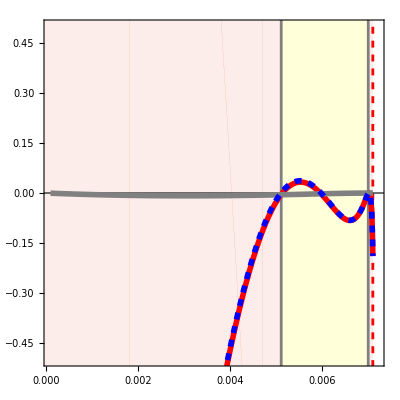

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[((L1*L2+L3)*L3)/L1^2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L4/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[OC/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.5,0.5}}]
```

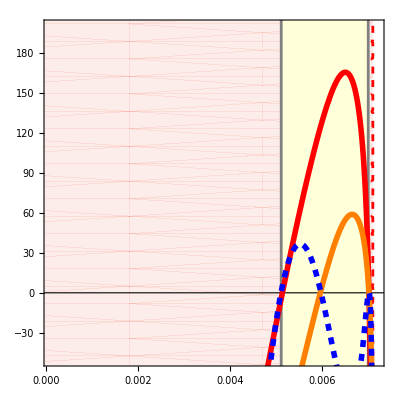

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L3*100/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->100],
Plot[OC*1000/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-50,200}}]
```

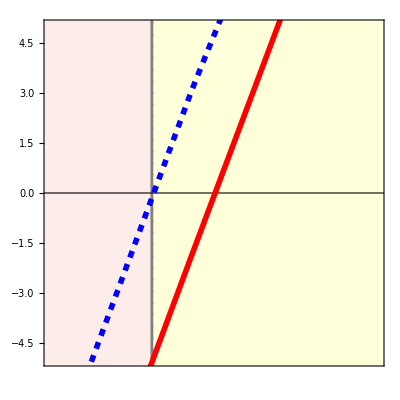

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},
PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->10,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[OC*1000/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->None,
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0050,0.0052},{-5,5}}]
```

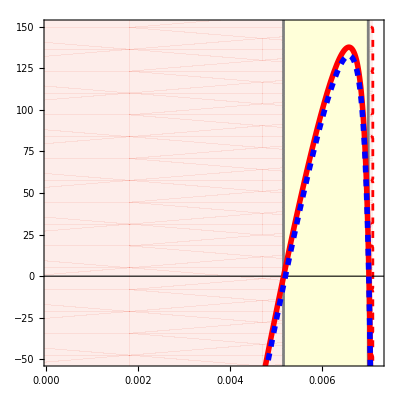

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

(*Plot[(J12*J21-J11*J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(J13*J31-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J11*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],*)
Plot[(-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
(*Plot[(-J22*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J22*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
*)
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-50,150}}]
```

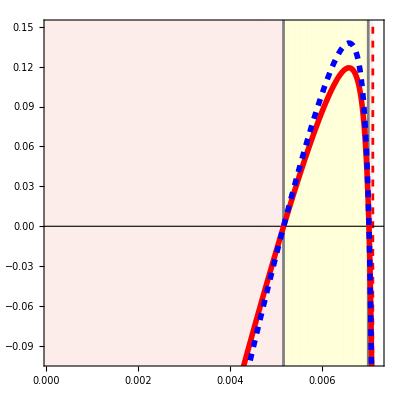

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],

Plot[-J11*J33*0.001/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100,PlotRange->All],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.1,0.15}}]
```

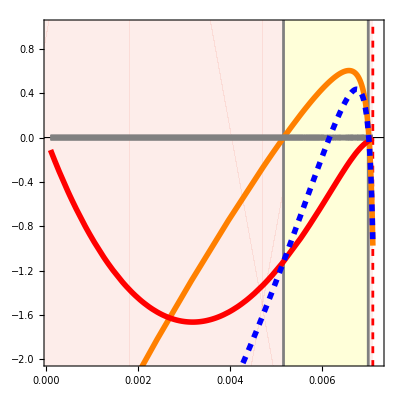

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

(*Plot[(J33 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.00779},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(J44 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.00779},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],*)
Plot[(J33 J44 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->10],
Plot[(-J34 J43 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J44 J21 J12)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J33 J21 J12 )/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->10],
Plot[(J33 J44 J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Rwed,Thickness->0.01},PlotPoints->10],
Plot[(-J34 J43 J22 )/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[L3/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-2,1}}]
```

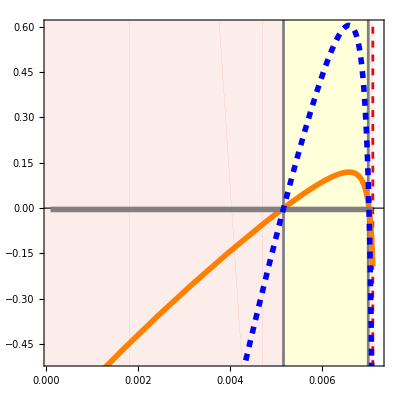

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->10],
Plot[(J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10, PlotRange->All],
Plot[(J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10,PlotRange->All],
Plot[J33 J44 J11/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.5,0.6}}]
```

#### ALL LOOPS

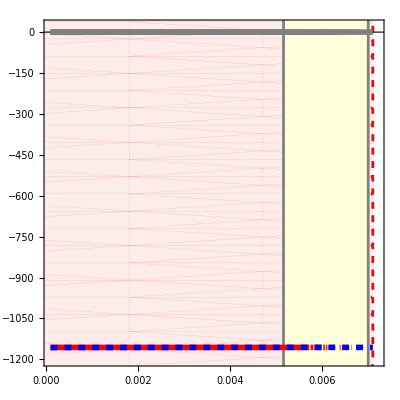

```mathematica
(* F1 *)
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-10000,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-10000,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[(J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],

Plot[L1/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-1200,20}}]
```

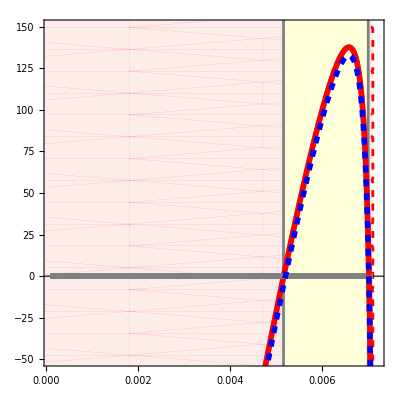

```mathematica
(* F2 *)
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J12*J21-J11*J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(J13*J31-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J11*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[(-J22*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J22*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],

Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-50,150}}]
```

```mathematica
(* F3 *)
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J33 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.00779},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(J44 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.00779},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(J33 J44 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->10],
Plot[(-J34 J43 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J44 J21 J12)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J33 J21 J12 )/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(J33 J44 J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J34 J43 J22 )/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[L3/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-2,1}}]
```

-Graphics-

```mathematica
(* F4 *)
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(-J34 J43 J12 J21)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(J33 J44 J12 J21)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->10],
Plot[(J34 J43 J22 J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[(-J11 J22 J33 J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->10],
Plot[L4/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.01,0.001}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.0071> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.007 > x>0.005105,{x,-0.01,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[L1/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L3*100/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Orange,Thickness->0.01},PlotPoints->100],
Plot[L4/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[OC*1000/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.0001,0.0071},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-50,150}}]
```

-Graphics-

### CHART - kz

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
DisplayBifurcationDiagram[FULL,kz,StateVariables->{V,P}, MaxSteps->Infinity, MinStepSize->0.1]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,kz}={105.937,0.0732854,99.9994,84.393,100}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,kz}={2354.53,0,99.9994,84.393,100}

-Graphics3D-

{}

```mathematica
Clear[kz]
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;dp=0.004; α=1; ω=4; δ=2;
```

```mathematica
solsKZ= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsKZ[[5]]/.kz->100
```

{V→,P→0.0568028,J→99.9994,M→84.393}

```mathematica
Vp = Re[solsKZ[[4,1,2]]];
Jp = Re[solsKZ[[4,3,2]]];
Mp = Re[solsKZ[[4,4,2]]];

Vo = Re[solsKZ[[5,1,2]]];
Po = Re[solsKZ[[5,2,2]]];
Jo = Re[solsKZ[[5,3,2]]];
Mo = Re[solsKZ[[5,4,2]]];

P0=(((yv ep)/yp)*((fvp β[Vp,Mp])/(hvp+ Vp β[Vp,Mp]))*Vp)/dp;
```

```mathematica
FindRoot[P0==1,{kz,2800}]
```

{kz→7822.08}

```mathematica
Show[
LogPlot[x=0,{x,-1,3100},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[x>78,{x,-100,3500},{y,-100,3000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[78>x>-100,{x,-100,2000},{y,-100,3000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->{LightYellow}],
LogPlot[x=0,{x,-1,3100},PlotStyle->{Black,Thickness[0.002]}],

LogPlot[Vo,{kz,1,3000},PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}, PlotPoints->500,PlotRange->All],
LogPlot[Jo,{kz,1,3000},PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}, PlotPoints->500,PlotRange->All],
LogPlot[Mo,{kz,1,3000},PlotStyle->{Black,Thickness[0.01]}, PlotPoints->500,PlotRange->All],
LogPlot[Po*1000,{kz,1,3000},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}, PlotPoints->500,PlotRange->All],


Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,2800},{3,8}}]
```

-Graphics-

### CHART - alpha

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
Quiet[DisplayBifurcationDiagram[FULL,α,MaxSteps->100000]]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={37.5,0.0267315,199.999,168.786,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={2354.53,0,199.999,168.786,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={2354.53,0,199.999,168.786,1}

-Graphics-

{BifurcationPoint[Hopf,{53.5266895460089,0.0378920588000257,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.004,dv→1/30,ep→0.09,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→0.256411295571395,δ→2,ω→4}]}

#### Population EQ

```mathematica
Clear[α];
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.004; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;  ω=4; δ=2;
```

```mathematica
solsFULL= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsFULL[[5]]/.α->0.4
```

{V→69.9827,P→0.0491872,J→199.999,M→168.786}

```mathematica
Va = Re[solsFULL[[5,1,2]]];
Pa = Re[solsFULL[[5,2,2]]];
Ja = Re[solsFULL[[5,3,2]]];
Ma = Re[solsFULL[[5,4,2]]];
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0.2564,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

LogPlot[Ja,{α,0.0001,0.5},PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}, PlotPoints->400],
LogPlot[Ma,{α,0.0001,0.5},PlotStyle->{Black,Thickness[0.01]}, PlotPoints->400],
LogPlot[Va,{α,0.0001,0.5},PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}, PlotPoints->400],
LogPlot[Pa*1000,{α,0.0001,0.5},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}, PlotPoints->400,PlotRange->All],

Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0,0.5},{0,6}}]
```

-Graphics-

#### MIN MAX MEAN

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
min = 0.005; max =0.5; gran = 0.005;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,α->i*gran},{{58.64,0.036,49.99,42.196}},200000,MaxSteps->500000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,α->i*gran},{Last[First[$Trajectories]]},20000, MaxSteps->Infinity, PlotPoints->1000];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0.2564,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0,0.5},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
Clear[α]
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.004; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;  ω=4; δ=2;
```

```mathematica
solsFULL= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsFULL[[10]]/.α->0.2
```

Part::partw: Part 10 of «1» does not exist.

Part::partw: Part 10 of {{V→0.,P→0.,J→199.999,M→168.786},{V→37.5,P→0.00725869,J→0.,M→0.},{V→666.667,P→0.,J→0.,M→0.},{V→2354.53,P→0.,J→199.999,M→168.786},{V→47.2609,P→0.0335475,J→199.999,M→168.786},{V→-22.5261-19.273 ⅈ,P→-0.0163592-0.0142281 ⅈ,J→199.999-3.825×10^-14 ⅈ,M→168.786-3.22805×10^-14 ⅈ},{V→-22.5261+19.273 ⅈ,P→-0.0163592+0.0142281 ⅈ,J→199.999+3.825×10^-14 ⅈ,M→168.786+3.22805×10^-14 ⅈ},{V→17.6456-29.343 ⅈ,P→0.0129512-0.0209368 ⅈ,J→199.999+0. ⅈ,M→168.786+0. ⅈ},{V→17.6456+29.343 ⅈ,P→0.0129512+0.0209368 ⅈ,J→199.999+0. ⅈ,M→168.786+0. ⅈ}} does not exist.

{{V→0.,P→0.,J→199.999,M→168.786},{V→37.5,P→0.00725869,J→0.,M→0.},{V→666.667,P→0.,J→0.,M→0.},{V→2354.53,P→0.,J→199.999,M→168.786},{V→47.2609,P→0.0335475,J→199.999,M→168.786},{V→-22.5261-19.273 ⅈ,P→-0.0163592-0.0142281 ⅈ,J→199.999-3.825×10^-14 ⅈ,M→168.786-3.22805×10^-14 ⅈ},{V→-22.5261+19.273 ⅈ,P→-0.0163592+0.0142281 ⅈ,J→199.999+3.825×10^-14 ⅈ,M→168.786+3.22805×10^-14 ⅈ},{V→17.6456-29.343 ⅈ,P→0.0129512-0.0209368 ⅈ,J→199.999+0. ⅈ,M→168.786+0. ⅈ},{V→17.6456+29.343 ⅈ,P→0.0129512+0.0209368 ⅈ,J→199.999+0. ⅈ,M→168.786+0. ⅈ}}⟦10⟧

```mathematica
(* All Levels *)
Show[
RegionPlot[5>x>0.2564,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[L1/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L2/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[L3/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L4/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[(OC/.solsFULL[[5]])*1000,{α,0.001,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.5},{-50,50}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* F1 *)
Show[
RegionPlot[5>x>0.2564,{x,-50,50},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564 > x>0,{x,-10,10},{y,-2000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(J11)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J22)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Red,Thickness[0.01]}, PlotPoints->100],
Plot[Re[(J44)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[L1/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,0.5},{-1200,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* F2 *)
Show[
RegionPlot[5>x>0.2564,{x,-5,5},{y,-200,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564> x>0,{x,-1,1},{y,-200,2000}, BoundaryStyle->{Gray},PlotPoints->10,PlotStyle->LightYellow],

Plot[Re[(J43*J34)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J12*J21)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11*J22)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J33*J44)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}, PlotPoints->200],
Plot[Re[(-J11*J44)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J22*J33)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J22*J44)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[(-J11*J33)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[L2/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,0.5},{-120,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

Power::infy: Infinite expression 1/0.^8 encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Show[
RegionPlot[5>x>0.2564,{x,-5,5},{y,-200,2000}, BoundaryStyle->RGBColor["#F05039"],PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564> x>0,{x,-1,1},{y,-200,2000}, BoundaryStyle->{Gray},PlotPoints->10,PlotStyle->LightYellow],

Plot[Re[(J11)*100/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Red,Thickness[0.01]}],

(*Plot[Re[(J33)*0.001/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33)*0.001/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Gray,Thickness[0.01]}],*)

Plot[Re[(-J11*J33)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,0.5},{-120,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True,AspectRatio->1,LabelStyle->16
]
```

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

-Graphics-

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>0.2564,{x,-5,5},{y,-200,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564 > x>0,{x,-1,1},{y,-200,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(-J34 J43 J22)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33 J44 J22)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J33 J21 J12)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[(- J44 J21 J12)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(- J34 J43 J11)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[( J33 J22 J11)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[( J44 J22 J11)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33 J44 J11)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[L3/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,0.5},{-2,1}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F4 *)
Show[
RegionPlot[5>x>0.2564,{x,-5,5},{y,-200,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.2564 > x>0,{x,-1,1},{y,-200,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(-J34 J43 J12 J21)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33 J44 J12 J21)/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(J34 J43 J22 J11)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(- J11 J22 J33 J44)/.solsFULL[[5]]],{α,0,0.5}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[L4/.solsFULL[[5]]],{α,0.001,0.5}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,0.5},{-0.008,0.001}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

Power::infy: Infinite expression 1/0.^8 encountered.

Power::infy: Infinite expression 1/0.^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

### CHART - omega

#### MIN MAX MEAN

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
min = 1; max =4; gran = 0.02;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,ω->i*gran},{{58.64,0.036,49.99,42.196}},100000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,ω->i*gran},{Last[First[$Trajectories]]},10000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];

]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 13490.1.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 13478.5.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 13850.1.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>1.706,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,3},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,3},{0,8}}]
```

-Graphics-

#### Population EQ

```mathematica
(* Manual recording of EQ values. omega not amenable to Dynamica or Mathematica Solve *)
```

```mathematica
DisplayPhasePortrait[FULL/.{ω->1.8},StateVariables->{V,P},PlotRange->All]
$PhasePortraitEPs
```

-Graphics-

{EquilibriumPoint[Saddle,Node,{0,0,199.999,168.786}],EquilibriumPoint[Stable,Mixed,{113.773,0.078432,199.999,168.786}],EquilibriumPoint[Saddle,Node,{2354.53,0,199.999,168.786}]}

```mathematica
(* HOPF: ω->1.706 *)
```

```mathematica
Vmeans[[All,1]]
```

{1.,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98,2.,2.02,2.04,2.06,2.08,2.1,2.12,2.14,2.16,2.18,2.2,2.22,2.24,2.26,2.28,2.3,2.32,2.34,2.36,2.38,2.4,2.42,2.44,2.46,2.48,2.5,2.52,2.54,2.56,2.58,2.6,2.62,2.64,2.66,2.68,2.7,2.72,2.74,2.76,2.78,2.8,2.82,2.84,2.86,2.88,2.9,2.92,2.94,2.96,2.98,3.,3.02,3.04,3.06,3.08,3.1,3.12,3.14,3.16,3.18,3.2,3.22,3.24,3.26,3.28,3.3,3.32,3.34,3.36,3.38,3.4,3.42,3.44,3.46,3.48,3.5,3.52,3.54,3.56,3.58,3.6,3.62,3.64,3.66,3.68,3.7,3.72,3.74,3.76,3.78,3.8,3.82,3.84,3.86,3.88,3.9,3.92,3.94,3.96,3.98,4.}

```mathematica
omegs = {1,1.1,1.2,1.3,1.4,1.5,1.6,1.7};
Vs = {100.488, 102.446, 104.31, 106.084, 107.773, 109.382, 110.915, 112.377};
Ps = {0.06968, 0.07098, 0.07221, 0.07338, 0.07449, 0.07555, 0.07656, 0.07752};
Js = {199.999,199.999,199.999,199.999,199.999,199.999,199.999,199.999};
Ms = {168.786,168.786,168.786,168.786,168.786,168.786,168.786,168.786};
```

```mathematica
omegfinal = Join[omegs,Vmeans[[All,1]][[37;;]]];
Vfinal = Join[Transpose[{omegs,Vs}],Vmeans[[37;;]]];
Pfinal = Join[Transpose[{omegs,Ps}],Pmeans[[37;;]]];
Jfinal = Join[Transpose[{omegs,Js}],Jmeans[[37;;]]];
Mfinal = Join[Transpose[{omegs,Ms}],Mmeans[[37;;]]];
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],


ListLogPlot[
Mfinal, PlotStyle->{Black,Thickness[0.01]},Joined->True, PlotRange->All],
ListLogPlot[
Jfinal, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]},Joined->True, PlotRange->All],
ListLogPlot[
Vfinal, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]},Joined->True, PlotRange->All],
ListLogPlot[
MapThread[List,{Pfinal[[All,1]],Pfinal[[All,2]]*1000}], PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},Joined->True, PlotRange->All],

PlotRange->{{1,3},{3,6}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True,AspectRatio->1
]
```

-Graphics-

#### Loops

```mathematica
Clear[ω];
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.004; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; δ=2; α=1;
```

```mathematica
omegfinal
```

{1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98,2.,2.02,2.04,2.06,2.08,2.1,2.12,2.14,2.16,2.18,2.2,2.22,2.24,2.26,2.28,2.3,2.32,2.34,2.36,2.38,2.4,2.42,2.44,2.46,2.48,2.5,2.52,2.54,2.56,2.58,2.6,2.62,2.64,2.66,2.68,2.7,2.72,2.74,2.76,2.78,2.8,2.82,2.84,2.86,2.88,2.9,2.92,2.94,2.96,2.98,3.,3.02,3.04,3.06,3.08,3.1,3.12,3.14,3.16,3.18,3.2,3.22,3.24,3.26,3.28,3.3,3.32,3.34,3.36,3.38,3.4,3.42,3.44,3.46,3.48,3.5,3.52,3.54,3.56,3.58,3.6,3.62,3.64,3.66,3.68,3.7,3.72,3.74,3.76,3.78,3.8,3.82,3.84,3.86,3.88,3.9,3.92,3.94,3.96,3.98,4.}

```mathematica
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegfinal,Re[((L1*L2+L3)*L3)/L1^2/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegfinal,Re[-L4/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegfinal,Re[OC/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,3},{-0.3,0.15}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegfinal,Re[L1/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegfinal,Re[L3/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegfinal,Re[L4/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegfinal,Re[L2/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]*0.1}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegfinal,Re[OC/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]*100}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,3},{-3,3}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F1 *)
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-2000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],


ListLinePlot[
Transpose[{omegfinal,Re[J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J22/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J33/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J44/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegfinal,Re[L1/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-1200,20}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F2 *)
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

(*ListLinePlot[
Transpose[{omegfinal,Re[J43*J34/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J12*J21/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J11 J22/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J33 J44/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J11 J44/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J22 J33/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J22 J44/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],*)
ListLinePlot[
Transpose[{omegfinal,Re[-J11 J33/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Red,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegfinal,Re[L2/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-100,60}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegfinal,Re[-J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J33/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegfinal,Re[-J11 J33/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]*0.001}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-0.1,0.1}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegfinal,Re[-J34 J43 J22/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J33 J44 J22/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J33 J21 J12/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Orange,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[- J44 J21 J12/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[- J34 J43 J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J33 J22 J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J44 J22 J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J33 J44 J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Red,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegfinal,Re[L3/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-2,0.5}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>1.706,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[1.706 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegfinal,Re[-J34 J43 J12 J21/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J33 J44 J12 J21/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[J34 J43 J22 J11/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegfinal,Re[-J11 J22 J33 J44/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegfinal,Re[L4/.{V->Vfinal[[All,2]], P->Pfinal[[All,2]],J->Jfinal[[All,2]], M->Mfinal[[All,2]], ω->omegfinal}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-0.008,0.001}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

### CHART - bj & dj

```mathematica
DisplayPhasePortrait[FULL/.{ep->0.06},StateVariables->{V,P}]
$PhasePortraitEPs
```

-Graphics-

{EquilibriumPoint[Saddle,Node,{0,0,199.999,168.786}],EquilibriumPoint[Saddle,Node,{305.811,0.1285,199.999,168.786}],EquilibriumPoint[Saddle,Node,{2354.53,0,199.999,168.786}]}

```mathematica
g=1/270; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=0.15; ω=4; δ=2;dp=0.004;
```

```mathematica
LH[b0_,dj0_]:=
Module[{bj=b0, djj = dj0},
b = bj;
dj = djj;
TS=NDSolveValue[
{ V'[t]==r*(1+δ M[t]/kz)*V[t]*(1 - V[t]/(kv*(1+δ M[t]/kz)))-((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],
J'[t]==b M[t](1-J[t]/kz) -g J[t] - dj J[t],
M'[t]==g J[t](1-M[t]/kz)- dm M[t],

V[0]==680,P[0]==0.5,J[0]==50, M[0]==50
},{V,P,J,M},{t,0,100000}];

Tout = Table[Evaluate[#[t]& /@TS],{t,50000,100000}];
peaks = FindPeaks[Tout[[All,1]], Automatic, Automatic, 0.1];
If[Length[peaks]>1,
per = peaks[[-1]][[1]]-peaks[[-2]][[1]];
out = Max[Tout[[All,1]][[peaks[[-2]][[1]];;peaks[[-1]][[1]]]]]-Min[Tout[[All,1]][[peaks[[-2]][[1]];;peaks[[-1]][[1]]]]];
max =  Max[peaks[[-2]][[2]];;peaks[[-1]][[2]]],

per = 0;
out = Max[Tout[[All,1]]];
max = Max[Tout[[All,1]]];
];

{per,out, Max[subs]}
]
```

```mathematica
granb = 100; (* 0.025 *)
grandj = 0.001; (* 0.0005 *)
startb = 1000;
startdj = 1/730;
maxb = 1500;
maxdj = 1/182; (* 0.115 *)
lifehist = {};
```

```mathematica
For[i=(startb/granb),i<=(maxb/granb),i++,
Clear[bin];
bin = i * granb;
For[j=(startdj/grandj),j<=(maxdj/grandj),j++,
Clear[djin];
djin = j * grandj;
AppendTo[lifehist,{bin, djin,LH[bin,djin]}];
]
]
```

```mathematica
lifehist[[All,3]]
```

{{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.21,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67},{1541,2247.2,2561.67}}

```mathematica
(* Max - Min I density (stability)*)
ListDensityPlot[ArrayReshape[lifehist[[All,3]][[All,1]],{IntegerPart[(maxb/granb) - (startb/granb)+1],IntegerPart[(maxdj/grandj)-(startdj/grandj)+1]}],DataRange->{{startb,maxb},{startdj,maxdj}},ColorFunction->(ColorData["TemperatureMap",#/2500.0]&),ColorFunctionScaling->False,
PlotLegends->Automatic, PlotRange->All,
FrameLabel->{"Dreissena birth rate", "Dreissena death rate"},LabelStyle->{Black,16}]
```

-Graphics-

```mathematica
(* Maximum I density *)
ListDensityPlot[ArrayReshape[lifehist[[All,3]][[All,2]],{IntegerPart[(maxb/granb) - (startb/granb)+1],IntegerPart[(maxdj/grandj)-(startdj/grandj)+1]}],DataRange->{{startb,maxb},{startdj,maxdj}},ColorFunction->(ColorData["TemperatureMap",#/2562]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->Automatic,
FrameLabel->{"Dreissena birth rate", "Dreissena death rate"},LabelStyle->{Black,16}]
```

-Graphics-

### CHART - ep

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
epBD1=Quiet[DisplayBifurcationDiagram[FULL/.{α->0.15},ep,MaxSteps->100000, StateVariables->{V,P}]]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ep}={2354.53,0,199.999,168.786,0.06}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ep}={2354.53,0,199.999,168.786,0.12}

-Graphics3D-

{BifurcationPoint[Hopf,{34.7827194408184,0.0290244169441328,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.004,dv→1/30,ep→0.105230401073152,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→0.15,δ→2,ω→4}]}

```mathematica
epBD2 = Quiet[DisplayBifurcationDiagram[FULL/.{α->0.15},ep,MaxSteps->100000, StateVariables->{J,M}]]
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ep}={2354.53,0,199.999,168.786,0.06}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ep}={2354.53,0,199.999,168.786,0.12}

-Graphics3D-

#### Population EQ

```mathematica
epBD1[[1]][[1]][[3]][[3]][[1]]
```

```mathematica
eps = Join[epBD1[[1]][[1]][[1]][[3]][[1]][[All,1]],epBD1[[1]][[1]][[2]][[3]][[1]][[All,1]]];
Vs = Join[epBD1[[1]][[1]][[1]][[3]][[1]][[All,2]],epBD1[[1]][[1]][[3]][[3]][[1]][[All,2]]];
Ps = Join[epBD1[[1]][[1]][[1]][[3]][[1]][[All,3]],epBD1[[1]][[1]][[3]][[3]][[1]][[All,3]]];
Js = Join[epBD2[[1]][[1]][[1]][[3]][[1]][[All,2]],epBD2[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ms = Join[epBD2[[1]][[1]][[1]][[3]][[1]][[All,3]],epBD2[[1]][[1]][[2]][[3]][[1]][[All,3]]];
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0.1052,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.1052> x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLogPlot[
Transpose[{eps,Ms}], PlotStyle->{Black,Thickness[0.01]},Joined->True, PlotRange->All],
ListLogPlot[
Transpose[{eps,Js}], PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]},Joined->True, PlotRange->All],
ListLogPlot[
Transpose[{eps,Vs}], PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]},Joined->True, PlotRange->All],
ListLogPlot[
Transpose[{eps,Ps*1000}], PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},Joined->True, PlotRange->All],

PlotRange->{{0.06,0.12},{0,7}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True,AspectRatio->1
]
```

Transpose::nmtx: The first two levels of {{0.12,0.119469703920666,0.117755418206381,0.116041132492095,0.114326846777809,0.112612561063523,0.110898275349238,0.109183989634952,0.107469703920666,0.105755418206381,«32»,0.105214089929923,0.105208985408903,0.10520388197812,0.105198779637238,0.105193678385924,0.105188578223841,0.105183479150658,0.105178381166038,«67273»},{0,0,«48»,«2208»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.12,0.11947,0.117755,0.116041,0.114327,0.112613,0.110898,0.109184,0.10747,0.105755,0.104041,0.102327,0.100613,0.0988983,0.097184,0.0954697,0.0937554,0.0920411,0.0903268,0.0886126,0.0868983,0.085184,0.0834697,0.0817554,0.0800411,0.0783268,0.0766126,0.0748983,0.073184,0.0714697,0.0697554,0.0680411,0.0663268,0.0646126,0.0628983,0.0612421,0.060414,0.06,0.06,0.10523,0.105224,0.105219,0.105214,0.105209,0.105204,0.105199,0.105194,0.105189,0.105183,0.105178,«67273»},{0.,0.,0.,0.,«43»,34.7712,34.7695,34.7678,«2208»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{0.12,0.119469703920666,0.117755418206381,0.116041132492095,0.114326846777809,«41»,0.105193678385924,0.105188578223841,0.105183479150658,0.105178381166038,«67273»},{0,0,«48»,«2208»}}^T is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

#### MIN MAX MEAN

```mathematica
DJac
```

{{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}}

```mathematica
Clear[ep];
```

```mathematica
min = 0.06; max =0.12; gran = 0.002;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,α->0.15,ep->i*gran},{{58.64,0.036,49.99,42.196}},100000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,α->0.15,ep->i*gran},{Last[First[$Trajectories]]},10000, MaxSteps->Infinity, MaxStepSize->0.1,PlotPoints->1000];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];

]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 39088.7.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 33605.4.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 29770.3.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0.1052,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.1052> x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0.06,0.12},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
Clear[ω];
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.004; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; δ=2; α=1;
```

```mathematica
omegs = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,1]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,1]]];
Vs = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,2]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ps = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,3]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,3]]];
Js = Join[OMBD2[[1]][[1]][[1]][[3]][[1]][[All,2]],OMBD2[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ms = Join[OMBD2[[1]][[1]][[1]][[3]][[1]][[All,3]],OMBD2[[1]][[1]][[2]][[3]][[1]][[All,3]]];
```

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[((L1*L2+L3)*L3)/L1^2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[-L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegs,Re[OC/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,3},{-0.15,0.05}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[L1/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L3/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.1}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegs,Re[OC/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*100}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,3},{-2,3}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F1 *)
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-2000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],


ListLinePlot[
Transpose[{omegs,Re[J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J22/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J44/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[L1/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-1200,20}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F2 *)
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[J43*J34/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J12*J21/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J11 J22/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J33 J44/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J11 J44/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J22 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J22 J44/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J11 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[L2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-100,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[-J11 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.001}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-0.1,0.1}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J34 J43 J22/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33 J44 J22/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J33 J21 J12/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Orange,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[- J44 J21 J12/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[- J34 J43 J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33 J22 J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J44 J22 J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33 J44 J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[L3/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-2,0.5}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>2.111,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.111 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J34 J43 J12 J21/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33 J44 J12 J21/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J34 J43 J22 J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[-J11 J22 J33 J44/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,3},{-0.008,0.001}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-